## Styling

```mathematica
dir=NotebookDirectory[]
```

/home/nicolas/git/talks/ICQ13 September 2016/talk/img/

```mathematica
(* Thickness *)
th=0.003;
```

```mathematica
(*Styling of the text*)
st=Directive[FontSize->15,FontFamily->"CMU Serif"];
stylize[text_]:=Style[text,st];
```

```mathematica
BostonBlue=RGBColor["#00688B"];
comp=RGBColor["#8B2300"];
```

```mathematica
SetOptions[ListPlot,Frame->True,FrameStyle->st,PlotRange->All];
```

## Link btw conumbering and gap labeling

This reasoning is due to Rémy Mosseri and Clément Sire.

Convergents
Let α_l be the lth convergent to the irrational number α. 
Ie α_l is the rational number obtained by truncating the continued fraction of α at the lth step.
A useful property of the convergents is that
If α_l= p_l/q_l then p_l q_(l+1)-p_(l+1)q_l = ±(-1)^l
which links them to the modular group.

Best approximants
We say that p/q is a best approximant of α if
|qα - p| < |q’α - p’| for all integers q’ < q, and for any integer p’. Note that in particular |α-p/q|< |α - p'/q'|.
Theorem: the best approximants are the convergents.

Conumbering
We introduce the approximant period b_l = (q_l, p_l) (written in the canonical basis of Z2) and the generator a_l = (q_l',p_l').
The generator is such that a_l and b_l form a basis of Z2, ie p_l' q_l-q_l' p_l = 1. We can thus use the convergents to construct the generator! The convergents have also the extra nice property that they are best approximants.
For a given point p ∈ Z2, we introduce the new integers c and k, such that:
c a_l + k b_l = p
c is the conumbering of p. The matrix U = [a_l,b_l] has the inverse U^-1={{-p_l, q_l}, {p_l', -q_l'}} and thus
c = n q_l mod n_l
where n=p_x+p_y, and p = (p_x,p_y).

Passing from normal to conumbering, and back
Since  p_l' q_l-q_l' p_l = 1 we have immediately that if
c = n q_l mod n_l
then
n = c (p_l'+q_l') mod n_l.

Gap labeling
The IDOS N(E) of E inside a gap of the lth approximant can be written
N_l(E)=(j(E))/n_l
where j(E) is the number of energy states below E.
Now, since gcd(p_l,q_l)=1, we can apply Bezout’s theorem and write j in the form
j=a q_l+b p_l = a q_l+b(n_l-q_l)=(a-b)q_l+b n_l 
where a = j p_l'+k p_l, b = -j q_l'-k q_l. (k is any integer).
From that, 
u = a - b = j (p_l'+q_l')  + k n_l = j (p_l'+q_l') mod n_l
Thus
N_l(E)=u q_l/n_l+b
The index b is nothing but a modulo 1 operation, and the index u plays the role of a normal numbering, while j plays the role of a conumbering.
Moreover, u is commonly referred to as the gap label of gap j.
It is interesting because it goes smoothly to the quasiperiodic limit (contrary to j).

```mathematica
octo[n_]:=octo[n]=2octo[n-1]+octo[n-2];
octo[0]=0;
octo[1]=1;
```

```mathematica
(* the metallic mean number we choose *)
metal[l_]:=Fibonacci[l]
```

```mathematica
(* p and q for metallic means series *)
p[l_]:=metal[l-2];
q[l_]:=metal[l-1];
(* number of atom per approximant *)
numb[l_]:=p[l]+q[l];
(* components of the generator, for metallic means series *)
pp[l_]:=(-1)^l p[l+1];
qq[l_]:=(-1)^l q[l+1];
(* pass from normal to conumbering and back *)
co[l_,n_]:=Mod[n q[l], numb[l]];
norm[l_,c_]:=Mod[c(pp[l]+qq[l]),numb[l]];
```

```mathematica
(* check that co and norm are inverse of each other *)
metal[l_]:=octo[l]
l=5;
COs=co[l,#]&/@Range[0,numb[l]-1]
Norms=norm[l,#]&/@COs
```

{0,12,7,2,14,9,4,16,11,6,1,13,8,3,15,10,5}

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}

The Hamiltonian of a periodic approximant

```mathematica
(* periodic approximant (of wavevector k) of a cut and project chain, in conumbering *)
h[l_,ρ_,k_]:=Block[{tblw,tbls,ar,n=numb[l],p=p[l],q=q[l]},
tblw=Table[{i,i+p}->ρ,{i,2,q}];
tbls=Table[{i,i+q}->1.,{i,1,p}];
PrependTo[tblw,{1,1+p}->Exp[I k]ρ];
ar=SparseArray[tblw,{n,n}]+SparseArray[tbls,{n,n}];
Normal[ar+ConjugateTranspose[ar]]
]
(* compute the energy bands *)
bands[l_,ρ_]:=Block[{vp,va},vp=Sort[Eigenvalues[h[l,ρ,0.]]];va=Sort[Eigenvalues[h[l,ρ,π]]];MapThread[{Min[#1,#2],Max[#2,#1]}&,{vp,va}]]
(* compute the energy bands specifying irrational α *)
bands[alpha_,l_,ρ_]:=Block[{α=alpha},bands[l,ρ]];
```

We investigate the behaviour of the gap widths as a function of the gap indices

```mathematica
metal[l_]:=Fibonacci[l];
l=15;
L=numb[l];
(* gap widths *)
bl=bands[l,0.5];
widths= Table[bl[[g+1,1]]-bl[[g,2]],{g,L-1}];
widths/=Min[widths];
(* gaps as circles in the (q, G(q)) plane, with radii reflecting the width of the gap *)
gapPts=Table[Disk[{j,gaplabel[l,j]},Abs@Log[widths[[j]]]],{j,1,L-1}];
Graphics[gapPts,Frame->True,FrameLabel->stylize/@{"g_l(u)","u"}]
```

-Graphics-

Cut and project

```mathematica
ClearAll[p,q,pp,qq,co,norm];
(* return Subscript[p, l] and Subscript[q, l] *)
pq[α_,l_]:=Through[{Numerator,Denominator}[Convergents[α,l-1][[l-1]]]]
p[l_]:=pq[α,l][[1]]
q[l_]:=pq[α,l][[2]]
(* number of atom per approximant *)
numb[l_]:=p[l]+q[l];
(* components of the generator, for metallic means series *)
pp[l_]:=(-1)^l p[l+1];
qq[l_]:=(-1)^l q[l+1];
(* pass from normal to conumbering and back *)
co[l_,n_]:=Mod[n q[l], numb[l]];
norm[l_,c_]:=Mod[c(pp[l]+qq[l]),numb[l]];
```

```mathematica
α=√2-1;
α=0.5(√5-1);
```

```mathematica
α=1./√2;
α=1./(√3+1);
```

```mathematica
(* return the gap label of the gap such that idos = j/L *)
gaplabel[l_,j_]:=Block[{u=norm[l,j],L=numb[l]},
If[u≤Floor[L/2],u,u-L]]
```

```mathematica
(* convert an Association to a List of Lists *)
AsList[a_Association]:=List@@@Normal[a]
```

Below we propose a quantitative criterion to check if a gap is permanent or not.
First, we remark that to each gap we can associate its unique gap label C such that 
idos_l(E∈gap) = C q_l/n_l+k
We compute the width of a gap:
Δ_l(C)=max(E∈gap)-min(E∈gap)
and its displacement:
D_l(C)=|<E>_(E∈C_(l+1))-<E>_(E∈C_l)|
We then say that a gap is permanent if its half width is larger than its displacement.

Below, we check numerically that this criterion yields the same permanent gaps as the criterion that they are iterates of the E=0 gap.
In fact, we only check that the detected number of stable gaps coincides with the predicted number.

```mathematica
α=0.5(√5-1);
l=16;
L=numb[l];
(* associate to each gap label the width of the gap *)
bl=bands[l,0.5];
widths=Association[Table[gaplabel[l,j]->bl[[j+1,1]]-bl[[j,2]],{j,L-1}]];
avE=Association[Table[gaplabel[l,j]->0.5(bl[[j+1,1]]+bl[[j,2]]),{j,L-1}]];

(* same things for the next approximant *)
l=l+1;
L=numb[l];
bl=bands[l,0.5];
avE2=Association[Table[gaplabel[l,g]->0.5(bl[[g+1,1]]+bl[[g,2]]),{g,L-1}]];

(* associate to each gap label the energy displacement of this gap from one approx to the next *)
disp=Association[Table[c->Abs[avE2[c]-avE[c]],{c,Keys[avE]}]];

(* test whether gaps are permanent or not *)
check=Table[{c,0.5widths[c]>disp[c]},{c,Keys[avE]}];
```

```mathematica
(* predicted number of stable gaps after l iterations of the Fibonacci rule *)
s[n_]:=s[n]=2s[n-2]+s[n-3]+2
s[1]=0;
s[2]=2;
s[3]=2;
(* check that the measured and predicted numbers coincide *)
{Count[Transpose[check][[2]],True],s[l-3]}
```

{754,754}

Now, we apply this practical criterion to the silver mean chain to detect the transient gaps.
We hope they will be the gaps with the largest index.

```mathematica
((n+√(n^2+4))/2)^-1/.n->3
%//Simplify
```

2/(3+√13)

2/(3+√13)

```mathematica
α=0.5(√5-1.);
chain="fibonacci";
l=17;
L=numb[l];
bl=bands[l,0.5];
widths=Association[Table[gaplabel[l,j]->bl[[j+1,1]]-bl[[j,2]],{j,L-1}]];
avE=Association[Table[gaplabel[l,j]->0.5(bl[[j+1,1]]+bl[[j,2]]),{j,L-1}]];

(* now compute the next bands *)
l2=l+1;
bl2=bands[l2,0.5];
L2=numb[l2];
avE2=Association[Table[gaplabel[l2,j]->0.5(bl2[[j+1,1]]+bl2[[j,2]]),{j,L2-1}]];
(* associate to each gap label the energy displacement of this gap from one approx to the next *)
disp=Association[Table[c->Abs[avE2[c]-avE[c]],{c,Keys[avE]}]];

(* test whether gaps are permanent or not *)
stable=Association[Table[c->0.5widths[c]>disp[c],{c,Keys[avE]}]];

(* divide by the smallest width so as to keep the log width well defined *)
m=Min[Values[widths]];
widths/=m;

gaps=Table[{If[stable[c],BostonBlue,comp],Point[{c,Abs@Log@widths[c]}]},{c,Keys[avE]}];
```

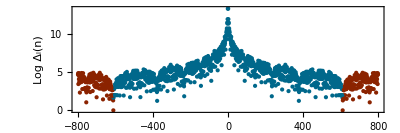

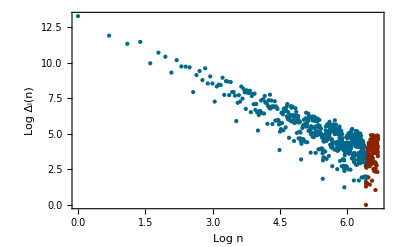

```mathematica
Graphics[{AbsolutePointSize[3.],gaps},Frame->True,FrameTicks->Automatic,FrameLabel->stylize/@{"n","Log Δ_l(n)"},AspectRatio->1/3]
Export[NotebookDirectory[]<>"loggapwidth_"<>chain<>"_l_"<>ToString[l]<>".pdf",%];
poslabs=Select[Keys[avE],#>0&];
loggaps=Table[{If[stable[c],BostonBlue,comp],Point[{Abs@Log@c,Abs@Log@widths[c]}]},{c,poslabs}];
Graphics[{AbsolutePointSize[3.],loggaps},Frame->True,FrameTicks->Automatic,FrameLabel->stylize/@{"Log n","Log Δ_l(n)"},AspectRatio->1/GoldenRatio]
Export[NotebookDirectory[]<>"logloggapwidth_"<>chain<>"_l_"<>ToString[l]<>".pdf",%];
```

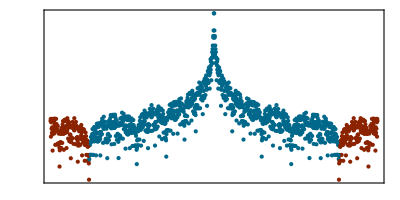

```mathematica
Graphics[{AbsolutePointSize[3.],gaps},Frame->True,FrameTicks->None,AspectRatio->1/2]
Export[NotebookDirectory[]<>"cover_illustration.pdf",%];
```